# Visualizing the Fourier Series For Curves

## Introduction

The goal of the project is to generate visualizations for how the Fourier series creates approximation of curves. The end result is a function that is able to generate two different graphics to show using Circles to represent the trigonometric waves used in the Fourier Series.The Fourier Series in Calculus is the summation of trigonometric waves in order to represent an approximation of a curve. Since the Fourier Series uses trigonometric functions which are created by the rotation of a circle, it is possible to link together multiple rotating circles and recreate the curve.

## Initial Attempts

#### Creating the Functions

I went through many iterations of my code an restarted on a new approach three times. The hardest part of this project was getting the information form the functions to be in a certain format so that it could be displayed in a cohesive manner. This issue rose form creating a generalized function that would work for most if not all scenarios.

#### Approach One

At first I tried to create multiple helper functions to manipulate the information and create it modular. The code below takes in a radius list, frequency list, and the number of circles needed, and then creates the nested list that is used for the moving objects in the graphics. The function is then called multiple times (I at that time had not optimized by code to run quickly) and used them to create list of Graphics Primitives. This one of the more developed versions of this method where the user physically inputs the amplitude and radii of the waves used to generate the desired function. In earlier versions I had an issue with getting animate to work; when I was not using slots in order to input lists and other information. I later found out that the function “Animate” had a “HoldAll” attribute which meant that it would not evaluate anything that is inputted directly in the Animate. Therefore, I had to adapt my code to evaluate outside the Animate and then be inserted into the Animate function via Slot Machines.

#### Approach Two

Although the previous method works, it is hard to know exactly if you are creating the desired function, Which means that you need to know what the radii/amplitudes and frequency where before you used this function.Hence my second approach.This approach was more of a function that would be built as an addition to the previous method.The new addition included a function built around the inbuilt function "FourierSeries" that took in function, variable, and number of terms as inputs and returned the equation of the approximation of the function as complex numbers.I had to use the inbuilt function "ComplexExpand" to get the equation in terms of Sine and Cosine.If the input function was even, then the Sine terms would cancel, and if the function is odd, then the Cosine terms canceled out.

## Function Definitions

### The Different Frequencies

I used a pair of functions called “FourierCosCoefficient” and “FourierSinCoefficient” in order separately get the radii of the circles. Then the many variables are used to artificially stitch together the coefficients and the frequencies; the code is using a descriete Fourier Transform, thus allowing me to artificially generate the frequencies used. Then the artificially generated Fourier series is used to generate coordinates. In the beginning I had the x coordinates to be in terms of Cosine and y coordinates in terms of Sine which caused the rotating parts to move in the counter clockwise direction. This function then creates individual moving plots which are then combined with the circles through the “Show” function to give the illusion that the circles are creating the plots. This function is named “unblendedCosCircleSmoothie” because this function returns the separate waves that were added to create the approximation, hence the “ingredients” in the “smoothie.” I created this function as a demonstration to show how separate waves and circles can create function when combined together; the different steps of the process would be a good visual aid in understanding the concept of what the Fourier Series does. Below there is an example of the function that is used for the even functions. For the odd functions I replaced a few operations and switched wherever it Cos to Sine and vise-versa.

#### Code Even Functions

This function uses Cosine waves in order to ad the frequencies. The inbuilt function “FourierCosCoefficient ”is used to generate a list of the radii/ amplitudes of the different frequencies.

```mathematica
ClearAll[unblendedCosCircleSmoothie]

unblendedCosCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot,totalRadius
		},
		(*This is used for the spacing of the rage of the graph*)
			totalRadius=Total[Abs@fourierCoeff];
	
		(*Creates a list of the circle fraphics primitives using the radii and a fixed coordinates*)
			circleList=Circle[{-maxRadius-5,0},#1]&/@Abs@fourierCoeff;
			
		(*sets up the coordinates that used to center and move different parts of the visual *)
			basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
			manipulatedCoord=Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}];
		
		(*Takes the maximum radius of the circles so that it can make use that none cross the y-axis*)
		maxRadius=Max[Abs@fourierCoeff];
		
		(*The following grouping of code implimets the necceary steps needed to create the rotating arms*)
			lineList=Line[{{-maxRadius-5,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
			styledLines=MapThread[Style,{lineList,color}];
			lineList=DeleteDuplicates[lineList];
		
		prePlot=MapThread[Times,{fourierCoeff,Cos[(Range[numCir]*(variable+$time))-(Pi/2)]}];
		
		(*The animate creates the visual. There is a heavy use of slot machines because of Animate's HoldAll property. 
		The slots make it such that everything is evaluaved outside the function.*)
			Animate[
				Show[
					Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
					Plot[#3,{variable,0,3*#5},PlotStyle->#4,PlotRange->All],PlotRange->All
					],
			{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color,totalRadius}]
	
	]
```

#### Code Odd Functions

This function uses Sine waves in order to ad the frequencies. The inbuilt function “FourierSinCoefficient “is used to generate a list of the radii/ amplitudes of the different frequencies. The Function below is around ninety-nine percent the same as the previous function, the the only difference being that the occurrences of Sine and Cosine are reversed.

```mathematica
ClearAll[unblendedSinCircleSmoothie]

unblendedSinCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierSinCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot,totalRadius
		},
		totalRadius=Total[Abs@fourierCoeff];
		maxRadius=Max[Abs@fourierCoeff]*1.5;
		circleList=Circle[{-maxRadius,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Sin[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius,basicCoord/.Sin->Cos}];
		
		lineList=Line[{{-maxRadius,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		lineList=DeleteDuplicates[lineList];
		prePlot=MapThread[Times,{fourierCoeff,Sin[(Range[numCir]*(variable+$time))+(Pi/2)]}];
		plotList=Plot[#1,{variable,0,10},PlotStyle->#2]&@@@(Transpose[{prePlot,color}]);
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				Plot[#3,{variable,0,3*#5},PlotStyle->#4,PlotRange->All],PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color,totalRadius}]
	
	]
```

### Circle Chains

The following function is structured similar to the previous algorithm. However, the difference is that now the centers of the circles are not static and are changed so that they create a chain. There is an algorithm that takes the set of coordinates and nests them together so that the circles follow an orbit. Another difference in this function is that instead of creating different rotating arms form the origin in order to color them, I was able to insert the entire nested function list into the line which created a line that appeared to be segmented. (The function that works for things that are not even or odd is a combination of the First tow algorithms. )

#### Circles for Even Functions

This function uses a similar pattern of code in order to link the circles together. Instead of creating centers of circles where the are the same every time this function nests the previous frequences which cause the circles to revolved in a linked manner.

```mathematica
ClearAll[circleCosSmoothie2]

circleCosSmoothie2[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierConstant=FourierCosCoefficient[function,variable,0]//ComplexExpand,
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,totalRadius,combinedCir,cirCenter,
		cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,
		lastXCoord,plotCoord,plotAllign
	
	
	},
	
	totalRadius=Total[Abs@fourierCoeff]*1.5;
	basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*$time]}];
	manipulatedCoord=Join[
		Take[
			Transpose[
			{(basicCoord-totalRadius)/.Cos->Sin,basicCoord}],1],
		Drop[Transpose[{basicCoord/.Cos->Sin,basicCoord}],1]];
	manipulatedCoord=Echo@(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Total[MapThread[Times,{fourierCoeff,Cos[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);
	lineSeries=DeleteCases[{lineSeries},_?(MatchQ[#[[1,-1]],{0,0}]&)];
	{
		Animate[
				Show[
					Graphics[{Sequence@@#1,#2},Axes->True],
					Plot[#3,{variable,0,3*#4},PlotRange->Full],
					PlotRange->{{-3*#4,3#4},{-#4,#4}}
					],
			{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord,totalRadius}],
		totalRadius
	}
	
	]
```

#### Circles for Odd Functions

```mathematica
ClearAll[circleSinSmoothie2]

circleSinSmoothie2[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierConstant=FourierSinCoefficient[function,variable,0]//ComplexExpand,
		fourierCoeff=Table[FourierSinCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,totalRadius,combinedCir,cirCenter,
		cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,
		lastXCoord,plotCoord
	
	},
	
	totalRadius=Total[Abs@fourierCoeff]*1.5;
	basicCoord=MapThread[Times,{fourierCoeff,Sin[Range[numCir]*$time]}];
	manipulatedCoord=Join[
		Take[
			Transpose[
			{(basicCoord-totalRadius)/.Sin->Cos,basicCoord}],1],
		Drop[Transpose[{basicCoord/.Sin->Cos,basicCoord}],1]];
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Total[MapThread[Times,{fourierCoeff,Sin[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);
	lineSeries=DeleteCases[{lineSeries},_?(MatchQ[#[[1,-1]],{0,0}]&)];

		{
			Animate[
					Show[
							Graphics[{Sequence@@#1,#2},Axes->True],
							Plot[#3,{variable,0,3*#4},PlotRange->Full],
							PlotRange->{{-3*#4,3#4},{-#4,#4}}
						],
				{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord,totalRadius}
					],totalRadius
		}
	]
```

#### Circles for Functions That are Not Even Or Odd

Unlike the other functions, this function uses the FourierSeries function and then extracts data from the equation itself (There are more detailed comment on what each step does in the code ). I turn the equation into a list and then separate the sine and cosine terms into different lists. Then a little bit more modification is needed to extract the coefficients which was done by replacing all the terms in a specific pattern to 1 so that it would multiply out and only leave me with the coefficients. Then I have functions similar to the previous ones which create a list of circle and line Graphics Primitives

```mathematica
ClearAll[circleSmoothietheRest]

circleSmoothietheRest[function_,variable_,numCir_]:=
Block[
{proto=FourierSeries[function,variable,numCir]//ComplexExpand,protoList2,cosList,sinList,cosCoeff,sinCoeff,
basicCosCoord,basicSinCoord,totalRadius,manipulatedCosCoord,manipulatedSinCoord,manipulatedCoord,
lastYCoord,plotCoord,cirCenter,cirArguments,lastLinetoYaxis,combinedCir,lineSeries,range,fourierCoeff},

protoList2=Drop[Apply[List,proto],1];
cosList=Take[protoList2,numCir];
sinList=(Apply[Plus,Partition[Drop[protoList2,numCir],2],{1}]);
cosCoeff=ReplaceAll[#1,Cos[x_]->1]&/@cosList;
sinCoeff=(ReplaceAll[#1,Sin[x_]->1]&/@sinList);
totalRadius=Echo@(Abs@(Total[Abs@cosCoeff]+Total[Abs@sinCoeff]));
fourierCoeff=Abs@Join[cosCoeff,sinCoeff];
	manipulatedCosCoord=Join[
		Take[
			Transpose[
			{(cosList-10)/.Cos->Sin,cosList}],1],
		Drop[Transpose[{cosList/.Cos->Sin,cosList}],1]];
	manipulatedSinCoord=Join[
		Take[
			Transpose[
			{(sinList-10)/.Sin->Cos,sinList}],1],
		Drop[Transpose[{sinList/.Sin->Cos,sinList}],1]];
	manipulatedCoord=(Join[manipulatedCosCoord,manipulatedSinCoord]/.x->$time);
	
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-10,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=(Total[cosList]+Total[sinList])/.variable->(variable+$time);
	cirCenter=Drop[manipulatedCoord,-1];
	(*I need to find a way to extract the radii of the Circles*)
	cirArguments=Transpose[{cirCenter,fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= (Line[#1]&@Evaluate[Append[manipulatedCoord,lastLinetoYaxis]]);
	
	range=(2Pi)*totalRadius;

	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,30},PlotRange->Full]
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord}]

]
```

### The Final Function

This function creates a Boolean expression which decides on which function to use by determine if the function that is inputted is Odd, Even, or neither. Then based on that evaluation, the corresponding function us called to generate the visual.

```mathematica
ClearAll[fourierCircleCookBook]
fourierCircleCookBook[function_,variable_Symbol,numCir_Integer]:=
Block[{cosAnimate,cosRadius,sinAnimate,sinRadius},
	{cosAnimate,cosRadius}=circleCosSmoothie2[function,variable,numCir];
	{sinAnimate,sinRadius}=circleSinSmoothie2[function,variable,numCir];
		Which[
		PossibleZeroQ[function-(function/.variable->(-variable))],
			Row[
				{unblendedCosCircleSmoothie[function,variable,numCir],
				cosAnimate,
				Plot[function,{variable,-3*cosRadius,3*cosRadius},PlotStyle->Black,Frame->True,ImageSize->Medium,Axes->False]}
				],
		PossibleZeroQ[function+(function/.variable->(-variable))],
			Row[
				{unblendedSinCircleSmoothie[function,variable,numCir],
				sinAnimate,
				Plot[function,{variable,-3*sinRadius,3*sinRadius},PlotStyle->Black,Frame->True,ImageSize->Medium,Axes->False]}
				],
		True,
			circleSmoothietheRest[function,variable,numCir]
		]
	]
```

## Some Example Tests

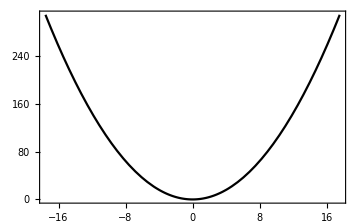

```mathematica
fourierCircleCookBook[x^2,x,5]
```

{{-8.78167,0},{-8.78167-4 Sin[$time],-4 Cos[$time]},{-8.78167-4 Sin[$time]+Sin[2 $time],-4 Cos[$time]+Cos[2 $time]},{-8.78167-4 Sin[$time]+Sin[2 $time]-4/9 Sin[3 $time],-4 Cos[$time]+Cos[2 $time]-4/9 Cos[3 $time]},{-8.78167-4 Sin[$time]+Sin[2 $time]-4/9 Sin[3 $time]+1/4 Sin[4 $time],-4 Cos[$time]+Cos[2 $time]-4/9 Cos[3 $time]+1/4 Cos[4 $time]},{-8.78167-4 Sin[$time]+Sin[2 $time]-4/9 Sin[3 $time]+1/4 Sin[4 $time]-4/25 Sin[5 $time],-4 Cos[$time]+Cos[2 $time]-4/9 Cos[3 $time]+1/4 Cos[4 $time]-4/25 Cos[5 $time]}}

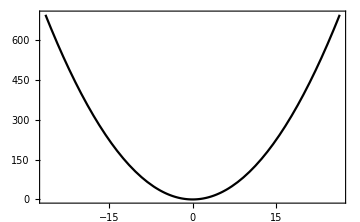

```mathematica
fourierCircleCookBook[x^2,x,5]
```

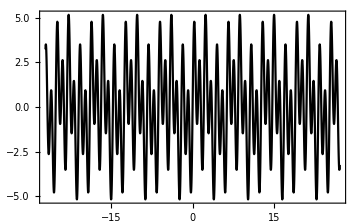

-Graphics-

```mathematica
fourierCircleCookBook[Sin[x]+2Sin[3x]+3Sin[6x],x,10]
```

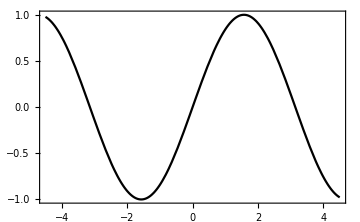

```mathematica
fourierCircleCookBook[Sin[x],x,1]
```

```mathematica
fourierCircleCookBook[x^3+x^2,x,5]
```

## Extension Development

### What if I want more of my Function to be created by the Fourier Series?

I would have to change the function before I create the circles. So if I want twice as much of my contain then f(x)->f(2x) and so on

### Tests on functions that are not entirely Odd or Even

```mathematica
fourierCircleCookBook[x^3-x,x,10]
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
fourierCircleCookBook[Cos[x]+2Cos[3x],x,20]
```

```mathematica
circleSmoothietheRest[x^3+x^2,x,5]
```

-16747/2000+(137 π^2)/30

## Non circle chain (unblended circles): In Development

example code to base it off of

```mathematica
ClearAll[unblendedCosCircleSmoothie]

unblendedCosCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot,totalRadius
		},
		totalRadius=Total[Abs@fourierCoeff];
		circleList=Circle[{-maxRadius-5,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}];
		maxRadius=Max[Abs@fourierCoeff];
		lineList=Line[{{-maxRadius-5,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		lineList=DeleteDuplicates[lineList];
		prePlot=MapThread[Times,{fourierCoeff,Cos[(Range[numCir]*(variable+$time))-(Pi/2)]}];
		plotList=Plot[#1,{variable,0,10},PlotStyle->#2]&@@@(Transpose[{prePlot,color}]);
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				Plot[#3,{variable,0,3*#5},PlotStyle->#4,PlotRange->All],PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color,totalRadius}]
	
	]
```

```mathematica
ClearAll[unblendedcircleSmoothietheRest]

unblendedcircleSmoothietheRest[function_,variable_,numCir_]:=
Block[
{proto=FourierSeries[function,variable,numCir]//ComplexExpand,
color=Drop[Hue[#]&/@Range[0,1,(1/(2*numCir))],-1],
protoList2,cosList,sinList,cosCoeff,sinCoeff,
basicCosCoord,basicSinCoord,totalRadius,manipulatedCosCoord,manipulatedSinCoord,manipulatedCoord,
lastYCoord,plotCoord,cirCenter,cirArguments,lastLinetoYaxis,combinedCir,lineSeries,range,fourierCoeff,lineList,styledLines,prePlot},

protoList2=Drop[Apply[List,proto],1];
cosList=Take[protoList2,numCir];
sinList=(Apply[Plus,Partition[Drop[protoList2,numCir],2],{1}]);
cosCoeff=ReplaceAll[#1,Cos[x_]->1]&/@cosList;
sinCoeff=(ReplaceAll[#1,Sin[x_]->1]&/@sinList);
totalRadius=Echo@(Abs@(Total[Abs@cosCoeff]+Total[Abs@sinCoeff]));
fourierCoeff=Abs@Join[cosCoeff,sinCoeff];
	manipulatedCosCoord=
			Transpose[
			{(cosList-10)/.Cos->Sin,cosList}];
	manipulatedSinCoord=
			Transpose[
			{(sinList-10)/.Sin->Cos,sinList}];
			
	manipulatedCoord=(Join[manipulatedCosCoord,manipulatedSinCoord]/.x->$time);
								
	lineList=Line[{{-10,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;			
	styledLines=MapThread[Style,{lineList,color}];					
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=(Total[cosList]+Total[sinList])/.variable->(variable+$time);
	cirCenter=Drop[manipulatedCoord,-1];
	(*I need to find a way to extract the radii of the Circles*)
	cirArguments=Transpose[{cirCenter,fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[{-10,0},#1]}&/@fourierCoeff;
	
	prePlot=protoList2/.variable->(variable+$time);
	
	range=(2Pi)*totalRadius;

	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,30},PlotRange->Full,PlotStyle->#4]
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,styledLines,prePlot,color}]

]
```

```mathematica
unblendedcircleSmoothietheRest[x^3+x^2,x,2]
```

-17/2+3 π^2

Transpose::nmtx: The first two levels of {{{-10-4 Sin[$time],-4 Cos[$time]},{-10+Sin[2 $time],Cos[2 $time]},{-10-12 Cos[$time]+2 π^2 Cos[$time],-12 Sin[$time]+2 π^2 Sin[$time]}},{4,1,-12+2 π^2,-3/2+π^2}} cannot be transposed.